```mathematica
SumDistance[L1_,L2_]:=(L1-0.5).(L2-0.5)
```

## Energy with k T

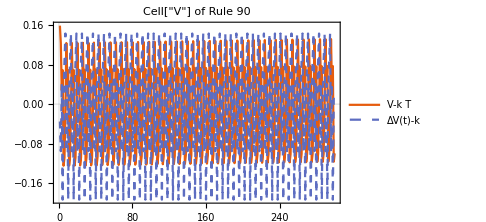
-Graphics- | -Graphics-

```mathematica
rule=90;
caData[]:=CellularAutomaton[rule,RandomInteger[{0,1},20],300];
caData[]:=#⟦1⟧&/@Partition[CellularAutomaton[rule,RandomInteger[{0,1},20],300],1];

energy=1/1000. Sum[Accumulate[HammingDistance@@@Partition[caData[],2,1]],{1000}];
(*energy=1/1000. Sum[Accumulate[SumDistance@@@Partition[caData[],2,1]],{1000}];*)
f=LinearModelFit[{Range[0,Length[energy]-1],energy}ᵀ⟦-Round[Length[energy]/3-1];;⟧,x,x];
energy2=(#⟦2⟧-f[#⟦1⟧])&/@({Range[0,Length[energy]-1],energy}ᵀ);
img=Grid@{{ListLinePlot[{energy2,Differences[energy]-f["BestFitParameters"]⟦2⟧},PlotRange->All,PlotLegends->{V-k T,ΔV[t]-k},PlotTheme->"Scientific",ImageSize->Medium,PlotLabel->StringTemplate["Cell["V"] of Rule ``"][rule],PlotStyle->{Automatic,Dashed}],ArrayPlot[CellularAutomaton[rule,RandomInteger[{0,1},100],99],PlotLabel->StringTemplate["Rule ``"][rule],ImageSize->Small]}}
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"img",StringTemplate["Energy_kT_rule``.pdf"][rule]}],img]
```

/Users/yanbozhang/项目 & 存档/01 科研项目/EnergyInCA/img/Energy_kT_rule90.pdf